# Singularities & The Point At Infinity

## October 28, 2020 - Covering Sections 5.6-5.7

### A point for discussion

Let’s talk about the coloring of these plots.  Earlier, I mentioned that they are related to the argument.  They are, but they indicate something a bit more.  They are actually encoding some information about “Poles” and “Zeros”

```mathematica
{{-Graphics-, , -Graphics-, , -Graphics-, , -Graphics-, , -Graphics-, -Graphics-}, {"zero", , "multiple zero", , "pole", , "multiple pole", , "essential singularity", }}
```

```mathematica
Test[zRange_]:=Module[{temp},
Print[zRange];
Print[zRange[[1]]]];
Test[{-3,3}]
```

{-3,3}

-3

```mathematica
ClearAll[PlotReIm]
```

```mathematica
PlotReIm[f0_,zRange_,plotOptions_]:=Module[{tmp,z,xmin,xmax,ymin,ymax,plotReal,plotImaginary,plotModulus},
z=zRange[[1]];
tmp[x_,y_]:=f0/.z->{x + I y};
xmin=Re[zRange[[2]]];
xmax = Re[zRange[[3]]];
ymin=Im[zRange[[2]]];
ymax =Im[zRange[[3]]];
plotReal = Plot3D[Re[tmp[x,y]],
{x,xmin,xmax},
{y,ymin,ymax},
PlotPoints->100,
ColorFunction->Function[{x,y,z},Hue[Arg[tmp[x,y]]/(2Pi)]],
ColorFunctionScaling->False,
Mesh->None,
PlotLabel->"Real Part of f(z)",
AxesLabel->{"x","y","Re(f(z))"},
plotOptions];
plotImaginary = Plot3D[Im[tmp[x,y]],
{x,xmin,xmax},
{y,ymin,ymax},
PlotPoints->100,
ColorFunction->Function[{x,y,u},Hue[Arg[tmp[x,y]]/(2Pi)]],
ColorFunctionScaling->False,
Mesh->None,
PlotLabel->"Im Part of f(z)",
AxesLabel->{"x","y","Im(f(z))"},
plotOptions];
plotModulus = Plot3D[Abs[tmp[x,y]],
{x,xmin,xmax},
{y,ymin,ymax},
PlotPoints->100,
plotOptions,
PlotRange->{0,10},
ColorFunction->Function[{x,y,u},Hue[Arg[tmp[x,y]]/(2Pi)]],
ColorFunctionScaling->False,
Mesh->None,
PlotLabel->"|f(z)|",
AxesLabel->{"x","y","|f(z)|"}];
GraphicsGrid[{{plotReal,plotImaginary,plotModulus}},ImageSize->Full]];
```

## Poles vs. Essential Singularities

```mathematica
PlotReIm[1/z,{z,-0.5-0.5I,0.5+0.5I},{PlotRange->Automatic}]
PlotReIm[1/z^2,{z,-0.5-0.5I,0.5+0.5I},{PlotRange->Automatic}]
PlotReIm[1/z^3,{z,-0.5-0.5I,0.5+0.5I},{PlotRange->Automatic}]
PlotReIm[1/z+1/(2z^2)+1/(6z^3),{z,-0.5-0.5I,0.5+0.5I},{PlotRange->Automatic}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotReIm[Exp[I/z],{z,-.25(1 + I),.25(1+I)},{PlotRange->Automatic,PlotLabel->"e^(1/z)"}]
```

-Graphics-

```mathematica
sVals =Flatten[{1,Table[{j,1/j},{j,2,5} ]}];
tVals = Table[-Pi+2Pi j/5,{j,0,4}];
GraphicsGrid[{{ContourPlot[Evaluate[Table[Abs[Exp[1/(x + I y)]]==s,{s,sVals}]],{x,-2,2},{y,-1,1},PlotLegends->sVals,ImageSize->Large,PlotPoints->100,PlotLabel->"Contours of Modulus"],ContourPlot[Evaluate[Table[Arg[Exp[1/(x + I y)]]==t,{t,tVals}]],{x,-1,1},{y,-2,2},PlotLegends->tVals,ImageSize->Large,PlotPoints->100,PlotLabel->"Contours of Arg"]}},ImageSize->Full]
```

-Graphics-

## Putting Things on The Riemann Sphere / The Point At Infinity

Now, let’s say that you wanted to see what happened as we consider points the Riemann Sphere.

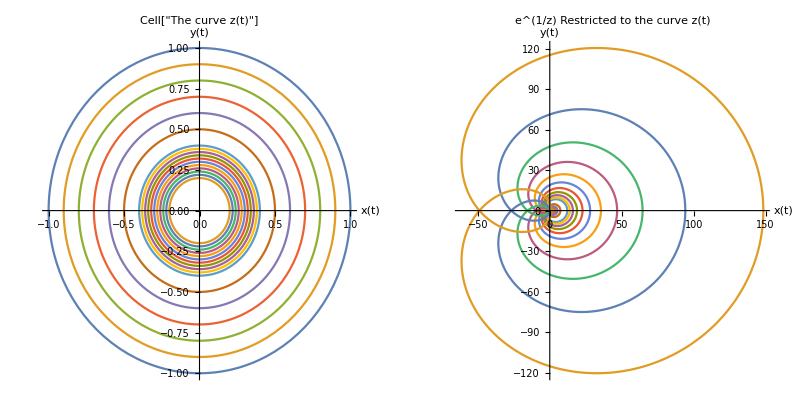

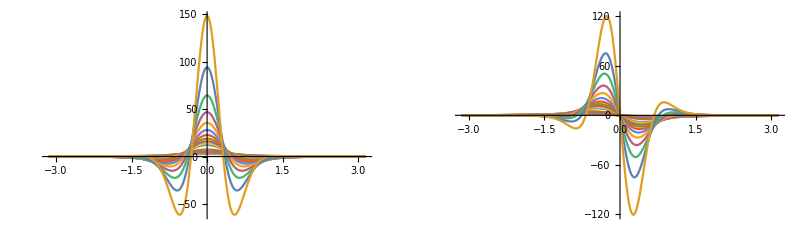

```mathematica
(*Define the point that you want to plot on the sphere*)
z [t_]=Exp[I t];
F[z_] = Exp[1/z];
rVals = Flatten[{Table[1-j/10.,{j,0,6}],Table[.4-j/50,{j,1,10}]}];
w=F[r z[t]];

zPlane=ParametricPlot[Evaluate[Table[{Re[r z[t]],Im[r z[t]]},{r,rVals}]],{t,-Pi,Pi},AxesLabel->{"x(t)","y(t)"},PlotStyle->Automatic,PlotPoints->100,PlotLabel->"Cell["The curve z(t)",ExpressionUUID->"b9754eee-6535-4985-8ecb-da4566ed9355"]"];

wPlane=ParametricPlot[Evaluate[Table[{Re[F[r z[t]]],Im[F[r z[t]]]},{r,rVals}]],{t,-Pi,Pi},AxesLabel->{"x(t)","y(t)"},PlotStyle->Automatic,PlotPoints->100,PlotLabel->"e^(1/z) Restricted to the curve z(t)",PlotRange->Full];
GraphicsGrid[{{zPlane,wPlane}}]
GraphicsGrid[{{Plot[Evaluate[Table[Re[F[r z[t]]],{r,rVals}]],{t,-Pi,Pi},PlotRange->Full],Plot[Evaluate[Table[Im[F[r z[t]]],{r,rVals}]],{t,-Pi,Pi},PlotRange->Full]}}]
```

```mathematica
(*The Sphere*)
sphere = ParametricPlot3D[{Sin[x]Sin[y],Cos[x]Sin[y],Cos[y]},{x,-Pi,Pi},{y,0,Pi},PlotStyle->Opacity[.1],ImageSize->Large,AspectRatio->1,AxesLabel->{"x","y","z"},Mesh->None,PlotPoints->100];

(*The Plane*)
plane = ParametricPlot3D[{x,y,0},{x,-5,5},{y,-5,5},PlotStyle->Opacity[.05],ColorFunction->"Rainbow",ImageSize->Large,Mesh->None];

(*The Equator*)
equator = ParametricPlot3D[{Cos[θ],Sin[θ],0},{θ,0,2Pi},PlotStyle->{Black,Thick}];

(*The Point in the Plane + the North pole*)
rVals = Table[1/2^j,{j,4,8}];
lineInPlane = ParametricPlot3D[Evaluate[Table[{Re[w],Im[w],0},{r,rVals}]],{t,-Pi,Pi}];

(*The point on the sphere*)
lineOnSphere = ParametricPlot3D[Evaluate[Table[1/(Abs[w]^2+1){2Re[w],2Im[w],Abs[w]^2-1},{r,rVals}]],{t,-Pi,Pi},PlotLegends->rVals,PlotPoints->100];
Show[sphere,lineOnSphere,plane,AspectRatio->1,PlotLabel->"The Riemann Sphere",ImageSize->Large]
```

-Graphics3D-